# Funcs

```mathematica
plotMoments[dir_,param_,timepoint_]:=Module[
{dirM,data,maxTime,rangeMin,rangeMax,range},
SetDirectory[NotebookDirectory[]];
dirM="../data/"<>dir<>"/moments/";
data=Import[dirM<>param<>"_"<>IntegerString[timepoint,10,5]<>".txt","Table"];
maxTime=data[[-1,1]];
rangeMin=Min[IntegerPart[100*Min[data[[;;,2]]]]/100-100,IntegerPart[100*Min[data[[;;,3]]]]/100-100];
rangeMax=Max[IntegerPart[100*Max[data[[;;,2]]]]/100+100,IntegerPart[100*Max[data[[;;,3]]]]/100+100];
range={rangeMin,rangeMax};

Return[ListLinePlot[{data[[;;,{1,2}]],data[[;;,{1,3}]]},
PlotRange->{{0,maxTime},range},
ImageSize->150
]];
];
```

```mathematica
fPlotAllMoments[dir_,param_,tStart_,tEnd_,tInterval_]:=Module[
{dirM,data,map},
dirM="../data/"<>dir<>"/moments/";
map=Association[];
Do[
data=Import[dirM<>param<>"_"<>IntegerString[t,10,4]<>".txt","Table"];
Do[
map[val[[1]]]=val[[{2,3}]];
,{val,data}];
,{t,tStart,tEnd,tInterval}];

Return[ListLinePlot[Transpose[Values[map]],
ImageSize->200
]]
];
```

# 1 hidden layer

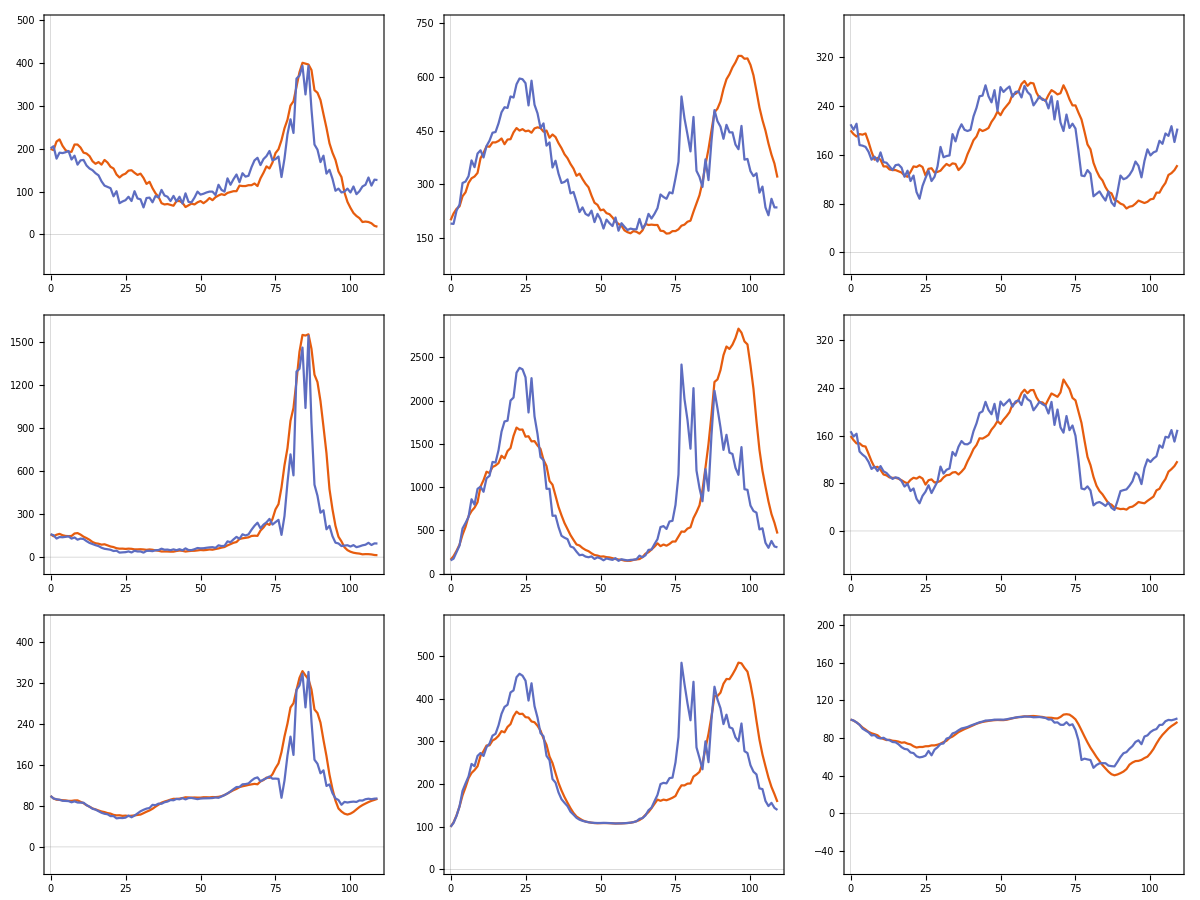

```mathematica
t=10000;
dirAM="learn_sequential";
Grid[{{plotMoments[dirAM,"hA",t],plotMoments[dirAM,"hB",t],plotMoments[dirAM,"hC",t]
},{plotMoments[dirAM,"wAX1",t],plotMoments[dirAM,"wBY1",t],plotMoments[dirAM,"wCZ1",t]
},{plotMoments[dirAM,"bX1",t],plotMoments[dirAM,"bY1",t],plotMoments[dirAM,"bZ1",t]
}}]
```

# 2 hidden layers

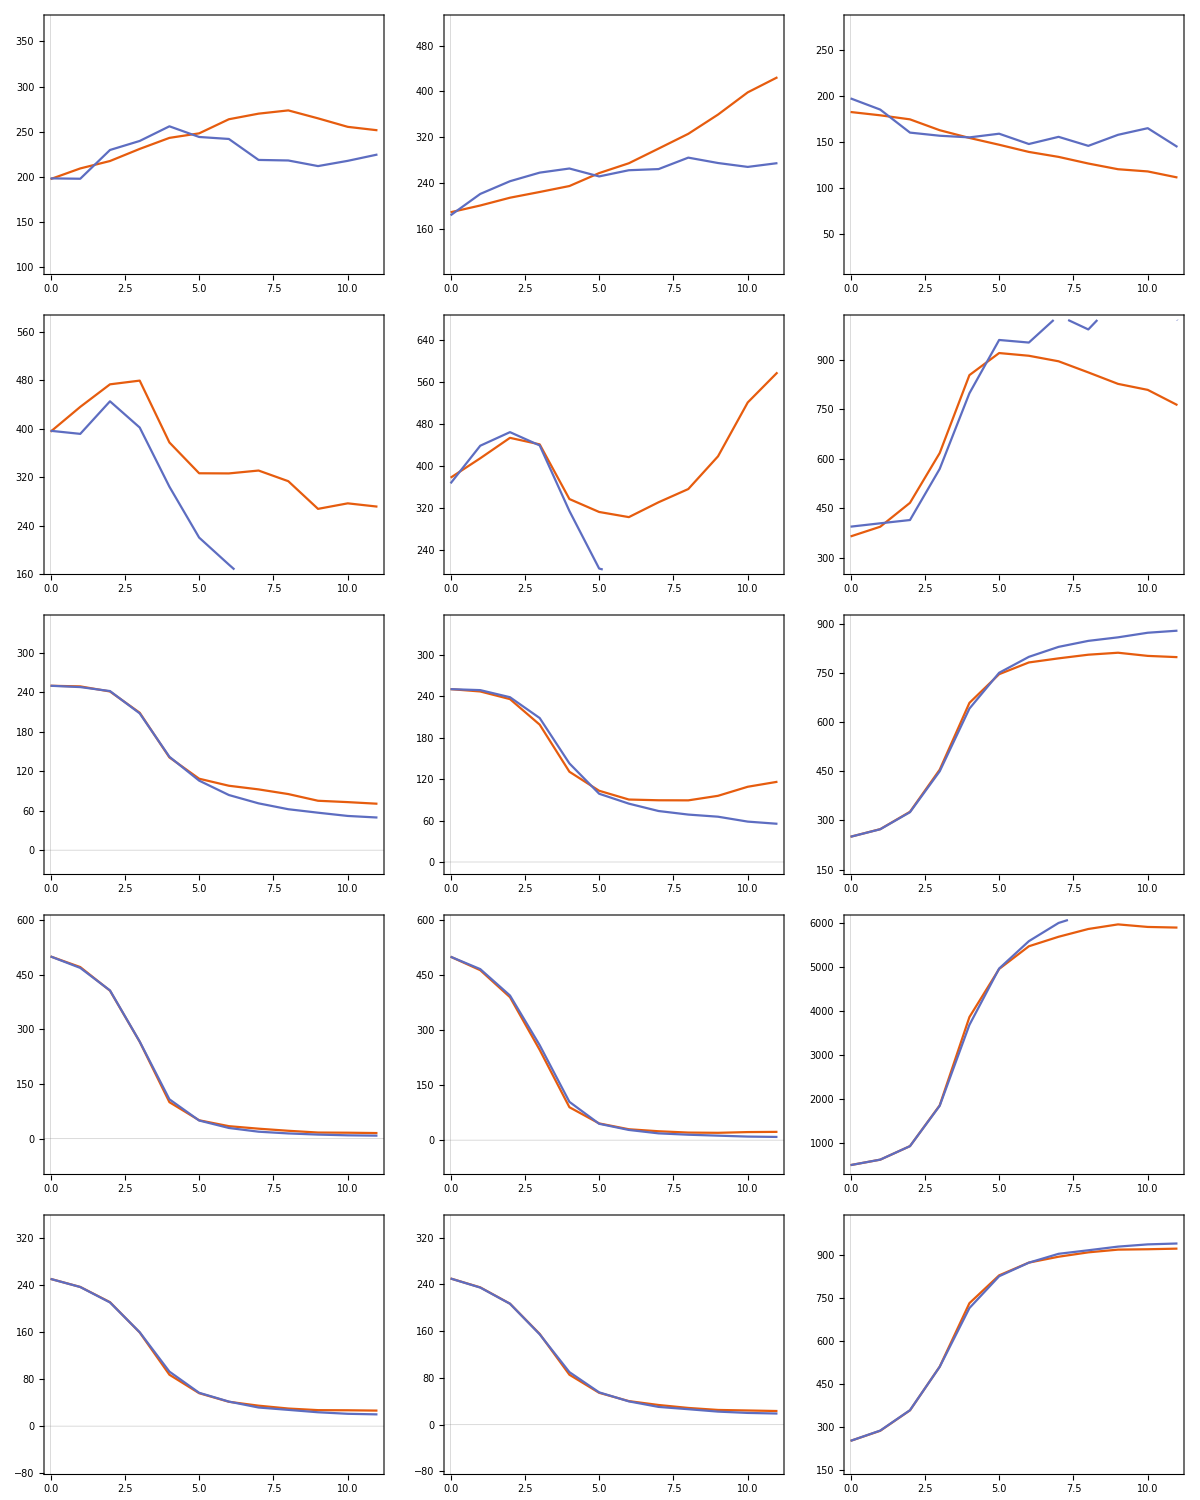

```mathematica
dirA="learn_traj_2layers";
t=680;
Grid[{{plotMoments[dirA,"hA",t],plotMoments[dirA,"hB",t],plotMoments[dirA,"hC",t]
},{plotMoments[dirA,"wAX1",t],plotMoments[dirA,"wBY1",t],plotMoments[dirA,"wCZ1",t]
},{plotMoments[dirA,"bX1",t],plotMoments[dirA,"bY1",t],plotMoments[dirA,"bZ1",t]
},{plotMoments[dirA,"wX1X2",t],plotMoments[dirA,"wY1Y2",t],plotMoments[dirA,"wZ1Z2",t]
},{plotMoments[dirA,"bX2",t],plotMoments[dirA,"bY2",t],plotMoments[dirA,"bZ2",t]
}}]
```